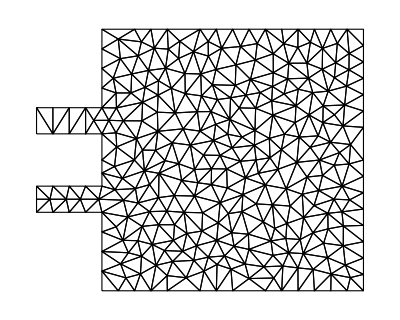

```mathematica
(* Start of given code *)
slits={Rectangle[{-0.25,0.3},{0, 0.4}],Rectangle[{-0.25,0.6},{0, 0.7}]};
square=Rectangle[{0,0},{1,1}];
Ω=RegionUnion[slits[[1]],slits[[2]],square];
Needs["NDSolve`FEM`"]
mesh=ToElementMesh[Ω, "MeshOrder"-> 1];
mesh["Wireframe"]
(*Remove semicolon for more detailed mesh*)
Show[mesh["Wireframe"["MeshElementIDStyle"->Red]],mesh["Wireframe"["MeshElement"->"PointElements","MeshElementIDStyle"->Blue]]];
nodes = mesh["Coordinates"];
elements = mesh["MeshElements"][[1,1]];
boundary =Flatten[mesh["BoundaryElements"][[1,1]]];
boundary=DeleteDuplicates[boundary];
Subscript[Γ, D]=Cases[nodes[[boundary]],{x_,_}/;x== -0.25];
boundNodes = Flatten[Nearest[nodes->"Index",Subscript[Γ, D],1]];
(* End of given code *)
```

```mathematica
(* Standard basis functions, i.e. shape functions *)
Subscript[ψ, 0][{ξ_,η_}]:=1-ξ-η
Subscript[ψ, 1][{ξ_,η_}]:=ξ
Subscript[ψ, 2][{ξ_,η_}]:=η
gradψ=Transpose@Grad[{Subscript[ψ, 0][{ξ,η}],Subscript[ψ, 1][{ξ,η}],Subscript[ψ, 2][{ξ,η}]},{ξ,η}];
gradψT=Transpose@gradψ;

(* The Jacobian and Jacobian inverse *)
(* Here we utilise the fact that R^2 vectors are represented as lists and we can directly get their "transpose" by using the list *)
J[elementNodes_]:={
elementNodes⟦2⟧-elementNodes⟦1⟧,
elementNodes⟦3⟧-elementNodes⟦1⟧}
B[elementNodes_]:={
{elementNodes⟦3,2⟧-elementNodes⟦1,2⟧,elementNodes⟦1,2⟧-elementNodes⟦2,2⟧},
{elementNodes⟦1,1⟧-elementNodes⟦3,1⟧,elementNodes⟦2,1⟧-elementNodes⟦1,1⟧}}

(* The local stiffness matrix *)
(* Formally, we would have to do something like this 
localStiffness[nodes_, element_]:=
1/(Det@J[nodes,element])NIntegrate[gradψT.(Transpose@B[nodes,element]).B[nodes,element].gradψ,{ξ,0,1},{η,0,1-ξ}]*)
(* However the integrand is constant so we just need to multiply it by the area of the standard triangle, which is 1/2 *)
localStiffness[elementNodes_]:=
0.5/(Det@J[elementNodes])gradψT.Transpose@B[elementNodes].B[elementNodes].gradψ
(* Same comments apply to localMass *)
localMass[elementNodes_]:=0.5Det@J[elementNodes]gradψT.gradψ


FEMMatrix[nodes_,elements_,localFunction_,nullNodes_]:=Module[{
globalMatrix = ConstantArray[0,{Length@nodes,Length@nodes}], element, stiffness},
For[k=1,k≤Length@elements,k++,
element = elements⟦k⟧;
stiffness=localFunction@nodes⟦element⟧;
For[i=1,i≤3,i++,
For[j=1,j≤3,j++,
globalMatrix⟦element⟦i⟧,element⟦j⟧⟧+=stiffness⟦i, j⟧;
];
];
];

(* We should now take into account that some of the coefficients will have to be 0 to ensure the boundary condition of u=0 *)
For[i=1,i≤Length@nullNodes,i++,
For[j=1,j≤Length@nodes,j++,
globalMatrix⟦j,nullNodes⟦i⟧⟧=0;
globalMatrix⟦nullNodes⟦i⟧,j⟧=0;
];
globalMatrix⟦nullNodes⟦i⟧,nullNodes⟦i⟧⟧=1;
];

globalMatrix
]

(* The function that assebles the global stiffness matrix *)
stiffnessMatrix[nodes_,elements_,nullNodes_]:=FEMMatrix[nodes,elements,localStiffness,nullNodes]

(* The function that assebles the global mass matrix *)
massMatrix[nodes_,elements_,nullNodes_]:=FEMMatrix[nodes,elements,localMass,nullNodes]

(* We will take the load vector to be 0 and just remove it from calculation. The 
loadVector=Table[0,Length@nodes];*)

ConcentrateMatrix[M_?MatrixQ]:=DiagonalMatrix[Total/@M]
ApproximateInverse[M_?MatrixQ]:=DiagonalMatrix[1/#&@*Total/@M]
```

```mathematica
solveEquation[T_,τ_]:=(
timeSteps=Ceiling@(T/τ);
(* We also assume u'(0, x̄) = 0 *)
sol=ConstantArray[0,{timeSteps, Length@nodes}];

For[k=1,k≤timeSteps,k++,
];

sol
)
```